```mathematica
$Assumptions = 0 <= θ <= 2Pi ;
ClearAll[g];
```

```mathematica
x = Sin[θ-Pi];
y = Cos[θ-Pi];
vx = D[x,θ] θ';
vy = D[y,θ]θ';
L = (1/2)(vx^2+vy^2)-g y//Simplify
H = (p θ' - L)/.Solve[ p == D[L, θ'], θ']//First//Simplify
```

g Cos[θ]+(θ')^2/2

1/2 (p^2-2 g Cos[θ])

```mathematica
act[en_] :=2 NIntegrate[ 1, {θ,p} ∈ ImplicitRegion[H < en, {{θ,0,2Pi},{p,0,1}}]]
```

```mathematica
4 Assuming[-1 <= en <= 1 && g > 0,Integrate[Sqrt[2en +2g  Cos[θ]], {θ, 0, Pi/2}]]
```

ConditionalExpression[(2 √2 (2 √(en (en+g)) EllipticE[(2 g)/(en+g)]+g HypergeometricPFQ[{1/4,3/4,1},{3/2,3/2},g^2/en^2]))/(√en), en>0]

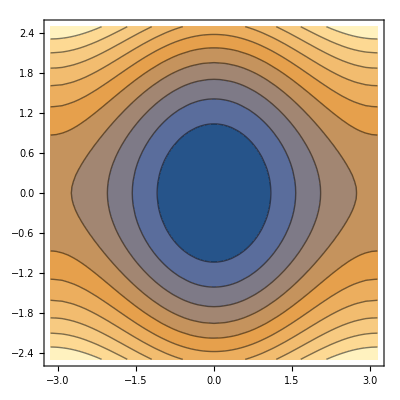

```mathematica
ContourPlot[H, {θ,-Pi,Pi}, {p, -2.5,2.5}, Contours->10]
```

```mathematica
act[-1]
act[0]
act[.9]
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

0.

5.60365

9.67809

```mathematica
pi = Plot[act[z], {z, -1,1}];
```

```mathematica
Solve[1/2 (p^2-2 g Cos[θ])==en, p]
```

{{p→-√2 √(en+g Cos[θ])},{p→√2 √(en+g Cos[θ])}}

```mathematica
Integrate[Sqrt[1 + Cos[x]],x]
```

2 √(1+Cos[x]) Tan[x/2]